```mathematica
TOP MASS EXTRACTION;
```

```mathematica
PSEUDO DATA GENERATOR;
```

IMPORTANT VARIABLES;

```mathematica
(*mt=173.2 GeV and Scale =173,2, invarian mass of tt bar*)
ClearAll["Global`*"]
SetDirectory[NotebookDirectory[]]
Needs["ErrorBarPlots`"]
Needs["HypothesisTesting`"]
mass={168.2, 170.7,173.2,175.7,178.2};
nmass=Length[mass];
number=3
npseudobin=20;
pvaluestandard=0.0455;
```

/mount/vol1/scratch/work/zam/top_mass_extraction/mathematica

3

```mathematica
DATA FROM HELAC (FOR STANDARD PSEUDODATA GENERATOR);
```

```mathematica
file=Table[FileNames[][[i+5]],{i,1,nmass}];
nbins=20;

start[n_]:=2+(n-1)*nbins
data=Block[{list},
list=Reap[Do[Sow[ReadList[file[[i]],{Number, Number, Number, Number}]],{i,1,nmass,1}]]][[2,1]];
datahist[ndiffdist_]:=Partition[Reap[Do[Block[{datalist},
datalist=Sow[data[[j,i]]];
],{j,1,nmass,1},{i, start[ndiffdist],start[ndiffdist]+nbins-1,1}]][[2,1]],nbins](*contains set of all histogram data for mtt bar for 5 different mass*)
crossection=Table[Reap[Do[Sow[data[[j,1]]],{j,1,nmass,1}]][[2,1,j,2]],{j,1,nmass}] (*fb*)
```

{951.072,930.023,906.377,882.921,859.732}

```mathematica
INPUT;
```

```mathematica
luminosity =35(*fb^-1*);
numbevents=Table[crossection[[i]]*luminosity*4,{i,1,Length[crossection]}];
stdnevents =Round[IntegerPart[numbevents[[number]]]/4]
numbofdiffdist1=9;
numbofdiffdist2=10;
numbofdiffdist=11;
nevents=20000;
int=2;
npseudo=100;
fit1={x,x^2}
fit2={x,x^2}
```

31723

{x,x^2}

{x,x^2}

```mathematica
NAMING SCHEME;
```

```mathematica
variable={"M_(t OverscriptBox[t, _])","p_(T, t) average", "p_(T, b OverscriptBox[b, _])", "M_b_1 average" , "M_(e^+)","M_(e^+)","M_(e^+)","min(M_(e^+),M_(e^+))","p_(T, SubscriptBox[b, 1])","p_(T, SubscriptBox[b, 2])","p_(T, b) average", "p_(T, SuperscriptBox[e, +])",
"p_(T, SuperscriptBox[μ, -])","p_(T, l) average", "p_(T, SuperscriptBox[e, +] SuperscriptBox[μ, -])","p_(T, SuperscriptBox[e, +] SubscriptBox[b, 1])","p_(T, SuperscriptBox[e, +] SubscriptBox[b, 2])", "p_(T, miss)","y_t average", "y_b average", "y_(e^+)","y_(μ^-)", "y_l average","y_(t OverscriptBox[t, _])","y_(b OverscriptBox[b, _])","ΔR_b_1","ΔR_(e^+)","ΔR_(e^+)","ΔR_(e^+)","ΔR_(μ^-)","ΔR_(μ^-)","ΔR_(t OverscriptBox[t, _])","y_(e^+)","p_(T, SubscriptBox[l, 1])","p_(T, SubscriptBox[l, 2])","y_l_1","y_l_2"};varnorm=Table["1/σ"<>ToString[(("d "σ)/("d" variable[[i]])),StandardForm],{i,1,Length[variable]}];
varname={"Mttbar","PTt_ave", "PTbbar","Mb1b2_ave","Me+b1","Me+b2","Me+mu-","min(Me+b1_Me+b2)","PTb1","PTb2","PTb_ave","PTe+","PTmu-","PTl_ave","PTe+mu-","PTe+b1","PTe+b2","PT_miss","yt_ave","yb_ave","ye+","ymu-","yl_ave","yttbar","ybbar","kdeltaRb1b2","kdeltaRe+mu-","kdeltaRe+b1","kdeltaRe+b2","kdeltaRmu-b1","kdeltaRmu-b2","kdeltaRttbar","ye+mu-","PTl1","PTl2","yl1","yl2"};
scalename={"et2","mt"};
scale={"E_T/2","mt"};
lum={"5 fb^-1","35 fb^-1"};
massname={"168,2","170,7","173,2","175,7","178,2"};
```

```mathematica
DATA LIST ;
```

```mathematica
bins=Partition[Block[{bin},
bin=Reap[Do[Sow[datahist[numbofdiffdist1][[i,j,1]]],{i,1,nmass,1},{j,1,Length[datahist[numbofdiffdist1][[i]]],1}]][[2,1]]],nbins];
binwidth=Table[(Max[bins[[i]]]-Min[bins[[i]]])/(nbins-1),{i,1,nmass}];
binsreal=Reap[Do[Sow[Chop[bins[[i]]-binwidth[[i]]/2]],{i,1,nmass,1}]][[2,1]];
Reap[Do[Sow[AppendTo[binsreal[[i]],Max[binsreal[[i]]]+binwidth[[i]]]],{i,1,nmass,1}]][[2,1]];
bwreal=Table[(Max[binsreal[[i]]]-Min[binsreal[[i]]])/(nbins),{i,1,nmass}];

valsdata[numbofdiffdist_]:=Partition[Block[{val},
val=Reap[Do[Sow[datahist[numbofdiffdist][[i,j,2]]],{i,1,nmass,1},{j,1,Length[datahist[numbofdiffdist][[i]]],1}]][[2,1]]],nbins];
valsn[numbofdiffdist_]:=Table[valsdata[numbofdiffdist][[i]]/(crossection[[i]]),{i,1,nmass}];(*normalised differential distribution : divided by 1/cross section *)

countsdata[numbofdiffdist_]:=Partition[Block[{count},
count=Reap[Do[Sow[datahist[numbofdiffdist][[i,j,4]]],{i,1,nmass,1},{j,1,Length[datahist[numbofdiffdist][[i]]],1}]][[2,1]]],nbins]
countsmax[numbofdiffdist_]:=Table[Sum[countsdata[numbofdiffdist][[i,j]],{j,1,Length[countsdata[numbofdiffdist][[i]]]}],{i,1,nmass}]
countsn[numbofdiffdist_]:=N[Table[countsdata[numbofdiffdist][[i]]/countsmax[numbofdiffdist][[i]],{i,1,nmass}]]

errordata[numbofdiffdist_]:=Partition[Block[{err},
err=Reap[Do[Sow[datahist[numbofdiffdist][[i,j,3]]],{i,1,nmass,1},{j,1,Length[datahist[numbofdiffdist][[i]]],1}]][[2,1]]],nbins];
errn[numbofdiffdist_]:=Table[errordata[numbofdiffdist][[i]]/(crossection[[i]]),{i,1,nmass}];
```

```mathematica
AVERAGE DATA LIST;
```

```mathematica
valsset=Reap[Do[Sow[{Reap[Do[Sow[valsdata[numbofdiffdist1][[i]]],{i,1,nmass,1}]][[2,1]][[j]],Reap[Do[Sow[valsdata[numbofdiffdist2][[i]]],{i,1, nmass,1}]][[2,1]][[j]]}],{j,1,nmass,1}]][[2,1]];
vals=Table[Reap[Do[Sow[Mean[valsset[[j]][[All,i]]]],{i,1,nbins,1}]][[2,1]],{j,1,nmass}];

valsnormset=Reap[Do[Sow[{Reap[Do[Sow[valsn[numbofdiffdist1][[i]]],{i,1,nmass,1}]][[2,1]][[j]],Reap[Do[Sow[valsn[numbofdiffdist2][[i]]],{i,1, nmass,1}]][[2,1]][[j]]}],{j,1,nmass,1}]][[2,1]];
valsnorm=Table[Reap[Do[Sow[Mean[valsnormset[[j]][[All,i]]]],{i,1,nbins,1}]][[2,1]],{j,1,nmass}];

errnormset=Reap[Do[Sow[{Reap[Do[Sow[errn[numbofdiffdist1][[i]]],{i,1,nmass,1}]][[2,1]][[j]],Reap[Do[Sow[errn[numbofdiffdist2][[i]]],{i,1, nmass,1}]][[2,1]][[j]]}],{j,1,nmass,1}]][[2,1]];
errnorm=Table[Reap[Do[Sow[Sqrt[(errnormset[[j,1,i]])^2+(errnormset[[j,2,i]])^2]],{i,1,nbins}]][[2,1]],{j,1,nmass}];

normalisation=Round[Table[Sum[valsnorm[[j,i]],{i,1,Length[valsnorm[[j]]]}]*binwidth[[j]],{j,1,nmass}]]

a=countsn[numbofdiffdist1];
b=countsn[numbofdiffdist2];
countsset=Reap[Do[Sow[{Reap[Do[Sow[a[[i]]],{i,1,nmass,1}]][[2,1]][[j]],Reap[Do[Sow[b[[i]]],{i,1, nmass,1}]][[2,1]][[j]]}],{j,1,nmass,1}]][[2,1]];
countsnorm=Table[Reap[Do[Sow[Mean[countsset[[j]][[All,i]]]],{i,1,nbins,1}]][[2,1]],{j,1,nmass}];
```

{1,1,1,1,1}

```mathematica
PROBABILITY DENSITY FUNCTION;
(*Weighted data by number of events*)
wdata=Block[{wdata},
wdata=Reap[Do[Sow[WeightedData[bins[[i]],vals[[i]]]],{i,1,nmass,1}]][[2,1]]
];
pdf=Block[{pdftest},
pdftest=Reap[Do[Sow[HistogramDistribution[wdata[[i]],{Min[binsreal[[i]]],Max[binsreal[[i]]],bwreal[[i]]}]],{i,1, nmass,1}]][[2,1]]
];
```

```mathematica
THE RATIO OF THE HELAC DATA(ALL NORMALIZED FIRST) ;
```

```mathematica
ratio=Block[{sortval,sortcount,maxval,posvalmax,maxcount,poscountmax,rat},
sortval=Reap[Do[Sow[Sort[valsnorm[[i]]]],{i,1,nmass,1}]][[2,1]];
sortcount=Reap[Do[Sow[Sort[countsnorm[[i]]]],{i,1,nmass,1}]][[2,1]];
maxval= Reap[Do[Sow[Max[sortval[[i]]]],{i,1,nmass,1}]][[2,1]];
posvalmax=Reap[Do[Sow[Flatten[Position[sortval[[i]],maxval[[i]]]]],{i,1,nmass,1}]][[2,1]];
maxcount= Reap[Do[Sow[Max[sortcount[[i]]]],{i,1,nmass,1}]][[2,1]];
poscountmax=Reap[Do[Sow[Flatten[Position[sortcount[[i]],maxcount[[i]]]]],{i,1,nmass,1}]][[2,1]];
rat=Flatten[Reap[Do[Sow[(sortval[[i,posvalmax[[i]]]]*bwreal[[i]])/sortcount[[i,poscountmax[[i]]]]],{i,1,nmass,1}]][[2,1]]]
]
```

{0.999627,0.999632,0.999602,0.999552,0.999528}

```mathematica
PSEUDO DATA -HISTOGRAM FITTING PROCEDURE FROM PDF (ASSUMPTION: SAME NUMBER OF BINS FROM HELAC AND RANDOM GENERATED HISTOGRAM);
```

```mathematica
HISTOGRAM GENERATED BY ARBITRARY EVENTS ACCORDING TO PDF;
```

```mathematica
histogram[nevents_,nmass_,binw_]:=Histogram[RandomVariate[pdf[[nmass]],nevents],{Min[binsreal[[nmass]]],Max[binsreal[[nmass]]],binw}] (*binw needs not the same with binsreal incase of different number of bins*)
listofhistogram[nevents_,nmass_,binw_]:=HistogramList[RandomVariate[pdf[[nmass]],nevents],{Min[binsreal[[nmass]]],Max[binsreal[[nmass]]],binw}]
```

```mathematica
NORMALIZATION OF HISTOGRAM;
```

```mathematica
histogramnorm[nevents_,nmass_,binw_]:=Histogram[WeightedData[bins[[nmass]],listofhistogram[nevents,nmass,binw][[2]]/nevents],{Min[binsreal[[nmass]]],Max[binsreal[[nmass]]],binw},PlotTheme->"Detailed"]
histogramlistnorm[nevents_,nmass_,binw_]:=N[HistogramList[WeightedData[bins[[nmass]],listofhistogram[nevents,nmass,binw][[2]]/nevents],{Min[binsreal[[nmass]]],Max[binsreal[[nmass]]],binw}]]
```

```mathematica
PSEUDODATA AND PSEUDOERRORS (FROM THE BEST THEORETICAL DATA OR PREDICTION  i e INV TTBAR );
```

```mathematica
pseudopointx[nevents_,nmass_,binw_]:=DeleteCases[histogramlistnorm[nevents,nmass,binw][[1]],Max[histogramlistnorm[nevents,nmass,binw][[1]]]]+bwreal[[nmass]]/2
pseudopointy[nevents_,nmass_,binw_]:=histogramlistnorm[nevents,nmass,binw][[2]]*ratio[[nmass]]/binw (*important to multiply by ratio!*)
pseudodata[nevents_,nmass_,binw_]:=N[MapThread[{#1,#2}&,{pseudopointx[nevents,nmass,binw],pseudopointy[nevents,nmass,binw]}]]

pseudoerror[nevents_,nmass_,binw_]:=Reap[Do[Sow[Sqrt[Variance[BernoulliDistribution[histogramlistnorm[nevents,nmass,binw][[2,i]]]]/nevents]*ratio[[nmass]]/binw],{i,1,nbins,1}]][[2,1]]
pseudo[nevents_,nmass_,binw_]:=Transpose[{pseudodata[nevents,nmass,binw][[All,1]],pseudodata[nevents,nmass,binw][[All,2]],pseudoerror[nevents,nmass,binw]}]
pseudoplot[nevents_,nmass_,binw_]:=ErrorListPlot[pseudo[nevents,nmass,binw],PlotTheme->"Detailed",PlotLabel-> "Pseudodata Points",PlotStyle->Red]
```

```mathematica
COMBINE HISTOGRAM FROM HELAC AND PSEUDODATA;
HELAC (THEORETICAL)  DATA LIST;
```

{1067.,1040.4,1013.99,985.914,960.451}

{1,1,1,1,1}

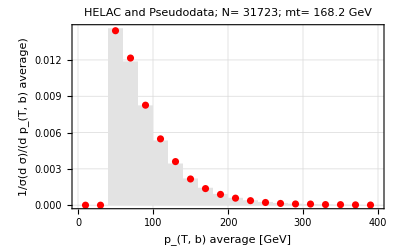
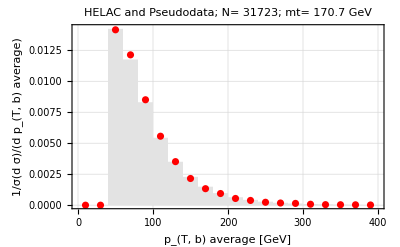
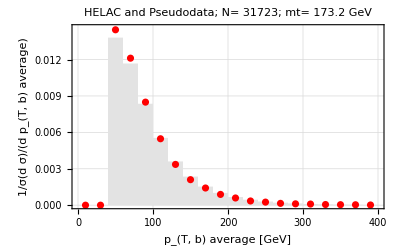
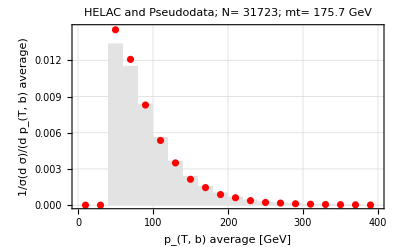
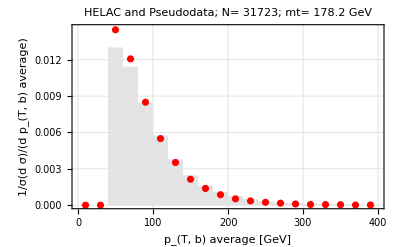

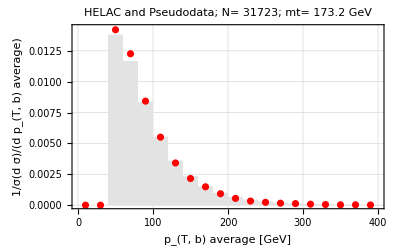

{0.,0.,0.0138069,0.0116711,0.00835619,0.00554588,0.00360249,0.00235588,0.00153132,0.00101054,0.000668092,0.000450165,0.000300499,0.000206693,0.00014554,0.0000987849,0.0000693301,0.0000473308,0.000034978,0.0000246537}

{0.,0.,0.287047,0.238975,0.172146,0.108975,0.0671122,0.0452038,0.0281814,0.0185985,0.011758,0.00775463,0.00539041,0.00334142,0.00182833,0.00119787,0.00107178,0.000693503,0.000472843,0.000252183}

{0.,0.,0.0144428,0.0120243,0.0083975,0.0055017,0.00348504,0.00214743,0.0014416,0.000902771,0.000578215,0.000384426,0.000253658,0.000167005,0.000094531,0.0000614451,0.0000346614,0.0000267838,0.0000189062,0.0000173307}

```mathematica
filehel=Table[FileNames[][[i]],{i,1,nmass}];

datahel=Block[{list},
list=Reap[Do[Sow[ReadList[filehel[[i]],{Number, Number, Number, Number}]],{i,1,nmass,1}]]][[2,1]];
datahisthel[ndiffdist_]:=Partition[Reap[Do[Block[{datalist},
datalist=Sow[datahel[[j,i]]];
],{j,1,nmass,1},{i, start[ndiffdist],start[ndiffdist]+nbins-1,1}]][[2,1]],nbins](*contains set of all histogram data for mtt bar for 5 different mass*)
crossectionhel=Table[Reap[Do[Sow[datahel[[j,1]]],{j,1,nmass,1}]][[2,1,i,2]],{i,1,nmass}] (*fb*)

binshel=Partition[Block[{bin},
bin=Reap[Do[Sow[datahisthel[numbofdiffdist][[i,j,1]]],{i,1,nmass,1},{j,1,Length[datahisthel[numbofdiffdist][[i]]],1}]][[2,1]]],nbins];
binwidthel=Table[(Max[binshel[[i]]]-Min[binshel[[i]]])/(nbins-1),{i,1,5}];
binsrealhel=Reap[Do[Sow[Chop[binshel[[i]]-binwidthel[[i]]/2]],{i,1,nmass,1}]][[2,1]];
Reap[Do[Sow[AppendTo[binsrealhel[[i]],Max[binsrealhel[[i]]]+binwidthel[[i]]]],{i,1,nmass,1}]][[2,1]];
bwrealhel=Table[(Max[binsrealhel[[i]]]-Min[binsrealhel[[i]]])/(nbins),{i,1,nmass}];

valsdatahel[numbofdiffdist_]:=Partition[Block[{val},
val=Reap[Do[Sow[datahisthel[numbofdiffdist][[i,j,2]]],{i,1,nmass,1},{j,1,Length[datahisthel[numbofdiffdist][[i]]],1}]][[2,1]]],nbins];
valsnhel[numbofdiffdist_]:=Table[valsdatahel[numbofdiffdist][[i]]/(crossectionhel[[i]]),{i,1,nmass}];(*normalised differential distribution : divided by 1/cross section *)

errordatahel[numbofdiffdist_]:=Partition[Block[{err},
err=Reap[Do[Sow[datahisthel[numbofdiffdist][[i,j,3]]],{i,1,nmass,1},{j,1,Length[datahisthel[numbofdiffdist][[i]]],1}]][[2,1]]],nbins];
errnhel[numbofdiffdist_]:=Table[errordatahel[numbofdiffdist][[i]]/(crossectionhel[[i]]),{i,1,nmass}];

HELAC (THEORETICAL) AVERAGE DATA LIST;
valssethel=Reap[Do[Sow[{Reap[Do[Sow[valsdatahel[numbofdiffdist1][[i]]],{i,1,nmass,1}]][[2,1]][[j]],Reap[Do[Sow[valsdatahel[numbofdiffdist2][[i]]],{i,1, nmass,1}]][[2,1]][[j]]}],{j,1,nmass,1}]][[2,1]];
valshel=Table[Reap[Do[Sow[Mean[valssethel[[j]][[All,i]]]],{i,1,nbins,1}]][[2,1]],{j,1,nmass}];

valsnormsethel=Reap[Do[Sow[{Reap[Do[Sow[valsnhel[numbofdiffdist1][[i]]],{i,1,nmass,1}]][[2,1]][[j]],Reap[Do[Sow[valsnhel[numbofdiffdist2][[i]]],{i,1, nmass,1}]][[2,1]][[j]]}],{j,1,nmass,1}]][[2,1]];
valsnormhel=Table[Reap[Do[Sow[Mean[valsnormsethel[[j]][[All,i]]]],{i,1,nbins,1}]][[2,1]],{j,1,nmass}];

errnormsethel=Reap[Do[Sow[{Reap[Do[Sow[errnhel[numbofdiffdist1][[i]]],{i,1,nmass,1}]][[2,1]][[j]],Reap[Do[Sow[errnhel[numbofdiffdist2][[i]]],{i,1, nmass,1}]][[2,1]][[j]]}],{j,1,nmass,1}]][[2,1]];
errnormhel=Table[Reap[Do[Sow[Sqrt[(errnormsethel[[j,1,i]])^2+(errnormsethel[[j,2,i]])^2]],{i,1,nbins}]][[2,1]],{j,1,nmass}];

normalisationhel=Round[Table[Sum[valsnormhel[[j,i]],{i,1,Length[valsnormhel[[j]]]}]*binwidthel[[j]],{j,1,nmass}]]


Which[int==1,
binhelac=bins;
valhelac=valsnorm;
binhelacreal=binsreal;
errorhelac=errnorm;
,
int==2,
binhelac=binshel;
valhelac=valsnormhel;                 (*can be different data from helac, ex: from different scale*)
binhelacreal=binsrealhel;
errorhelac=errnormhel;
]


histfromhelac[nmass_]:=Histogram[WeightedData[binhelac[[nmass]],valhelac[[nmass]]],{binhelacreal[[nmass]]},PlotTheme->"Detailed",ChartBaseStyle->EdgeForm[None],ChartStyle->GrayLevel[0.89]]
histfromhelaclist[nmass_]:=HistogramList[WeightedData[binhelac[[nmass]],valhelac[[nmass]]],{binhelacreal[[nmass]]}]

combine[nevents_,nmass_,binw_]:=Show[histfromhelac[nmass],pseudoplot[nevents,3,binw],
PlotTheme->"Detailed",
PlotLabel-> StringForm["HELAC and Pseudodata; N= ``; mt= `` GeV",nevents, mass[[nmass]]],
FrameLabel-> {StringForm["`` [GeV]",variable[[numbofdiffdist]]],StringForm["``",varnorm[[numbofdiffdist]]]}
]

pt5=Table[combine[stdnevents,i,(binwidth[[i]]*nbins/npseudobin)],{i,1,nmass}]
pt1=combine[Round[stdnevents],3,(binwidth[[3]]*nbins/npseudobin)]
valhelac[[3]]
histogramlistnorm[stdnevents,3,binwidth[[3]]][[2]]
pseudopointy[stdnevents,3,binwidth[[3]]]
```

```mathematica
THE  TOP MAS EXTRACTION PART;
```

```mathematica
FITTING THE VALUE OF DIFFERENTIAL VARIABLE FROM HELAC (THEORY) FOR EACH BIN FOR FIVE MASSES;
```

```mathematica
THEORETICAL VALUES AND ERRORS EXCEPT THE ZEROES ONE;
```

```mathematica
valsnormtheo=Reap[Do[Sow[valhelac[[All,i]]],{i,1,nbins,1}]][[2,1]]*(binwidthel[[1]]*nbins/npseudobin); (*the integrated value/area under the bar*)
errnormtheo=Reap[Do[Sow[errorhelac[[All,i]]],{i,1,nbins,1}]][[2,1]]*(binwidthel[[1]]*nbins/npseudobin);

valsbindata[int_]:=Reap[Do[Sow[{{mass[[i]],valsnormtheo[[int,i]]},ErrorBar[errnormtheo[[int,i]]]}],{i,1,nmass,1}]][[2,1]]; (*for graph*)
valsbindatanozero=Reap[Block[{valerr,nol},
valerr=Table[valsbindata[i],{i,1,nbins}];
nol=Table[{{mass[[k]],0.},ErrorBar[0.]},{k,1,nmass}];
Sow[DeleteCases[valerr,nol]]]][[1]];

valsbintheo[int_]:=Reap[Do[Sow[{{mass[[i]],valsnormtheo[[int,i]]},errnormtheo[[int,i]]}],{i,1,nmass,1}]][[2,1]] (*{mass,vals},err*)
valsbintheonozero=Reap[Block[{valerrtheo,nol},           (*{mass,vals},err NON ZERO BIN*)
valerrtheo=Table[valsbintheo[i],{i,1,nbins}];
nol=Table[{{mass[[k]],0.},0.},{k,1,nmass}];
Sow[DeleteCases[valerrtheo, nol]]]][[1]];
```

```mathematica
NON ZERO BIN ENTRIES;
```

```mathematica
nonzerobin=If[MemberQ[Flatten[Transpose[valsnormtheo]],0.]==False,{"nothing"},
Block[{valstheo,errtheo,zero,nonzero,all,comp},
valstheo=Transpose[valsnormtheo];
errtheo=Transpose[errnormtheo];
zero=Reap[Do[If[valstheo[[i,j]]== 0 && errtheo[[i,j]]== 0,
Sow[{i,j}],Nothing],{i,1,nmass,1},{j,1,nbins,1}]
][[2]];
all=Flatten[Table[{Range[nmass][[i]],Range[nbins][[j]]},{i,1,nmass},{j,1,nbins}],1];
comp=Complement[all,zero[[1]]];
nonzero=If[zero≠ {},Reap[Sow[comp]],
Nothing]
][[1]]
]
```

{{1,3},{1,4},{1,5},{1,6},{1,7},{1,8},{1,9},{1,10},{1,11},{1,12},{1,13},{1,14},{1,15},{1,16},{1,17},{1,18},{1,19},{1,20},{2,3},{2,4},{2,5},{2,6},{2,7},{2,8},{2,9},{2,10},{2,11},{2,12},{2,13},{2,14},{2,15},{2,16},{2,17},{2,18},{2,19},{2,20},{3,3},{3,4},{3,5},{3,6},{3,7},{3,8},{3,9},{3,10},{3,11},{3,12},{3,13},{3,14},{3,15},{3,16},{3,17},{3,18},{3,19},{3,20},{4,3},{4,4},{4,5},{4,6},{4,7},{4,8},{4,9},{4,10},{4,11},{4,12},{4,13},{4,14},{4,15},{4,16},{4,17},{4,18},{4,19},{4,20},{5,3},{5,4},{5,5},{5,6},{5,7},{5,8},{5,9},{5,10},{5,11},{5,12},{5,13},{5,14},{5,15},{5,16},{5,17},{5,18},{5,19},{5,20}}

```mathematica
FITTING FUNCTIONS;
```

```mathematica
value=Reap[Do[Sow[valsbintheonozero[[i]][[All,1]]],{i,1,Length[valsbintheonozero],1}]][[2,1]];
err=Reap[Do[Sow[valsbintheonozero[[i]][[All,2]]],{i,1,Length[valsbintheonozero],1}]][[2,1]];

(*value1=Reap[Do[Sow[valsbintheonozero[[i]][[All,1]]],{i,1,Length[valsbintheonozero],1}]][[2,1]];
err1=Reap[Do[Sow[valsbintheonozero[[i]][[All,2]]],{i,1,Length[valsbintheonozero],1}]][[2,1]];
value=Table[Cases[value1[[i]],Except[value1[[i,3]]]],{i,1,Length[value1]}];
err=Table[Cases[err1[[i]],Except[err1[[i,3]]]],{i,1,Length[err1]}];*)


fitting=Which[valhelac==valsnorm,
LinearModelFit[value[[#]],fit1,x,Weights->1/(err[[#]])^2]&/@ Range[1,Length[value]],
valhelac==valsnormhel,
LinearModelFit[value[[#]],fit2,x,Weights->1/(err[[#]])^2]&/@ Range[1,Length[value]]
];


(*fitting=LinearModelFit[value[[#]],{x,x^2,x^3,x^4},x,Weights->1/(err[[#]])^2]&/@ Range[1,Length[value]];*)
```

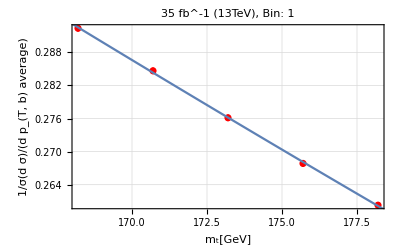
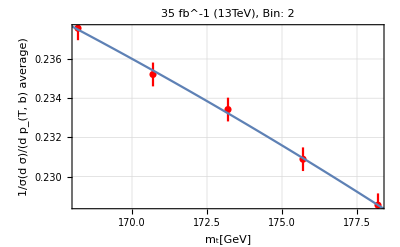
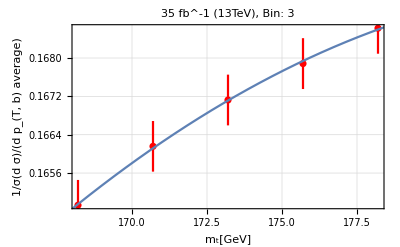
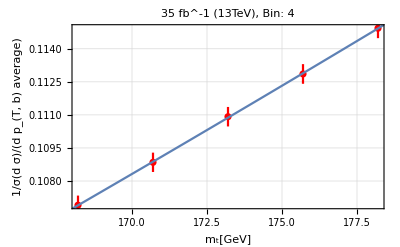
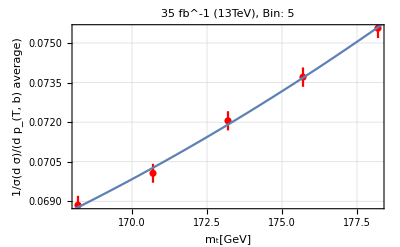
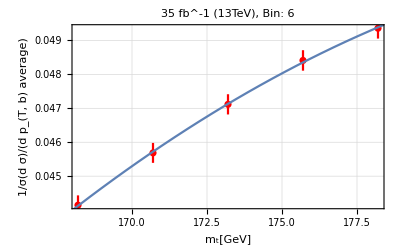
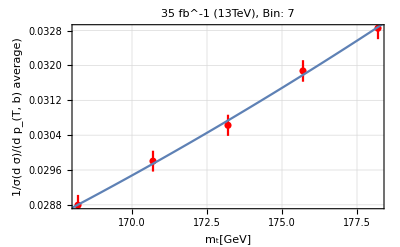
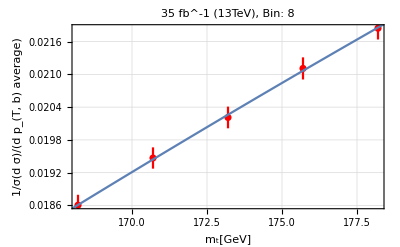

```mathematica
valsbinplot[int_]:=ErrorListPlot[valsbindatanozero[[int]],PlotTheme->"Detailed",PlotLabel-> StringForm["`` fb^-1 (13TeV), Bin: ``",luminosity,int],PlotStyle->Red]
funcfit[int_]:=Normal[fitting[[int]]]
funcbin[int_,nmass_]:=funcfit[int]/.x-> mass[[nmass]]
combbinfunc[int_]:=Block[{func},
func=funcfit[int]; (*fitting with polynomial arbitrary order*)
Show[valsbinplot[int],Plot[func,{x,160,180}],FrameLabel->{"m_t[GeV]",StringForm["``",varnorm[[numbofdiffdist]]]}]
]
allfit=Table[combbinfunc[i],{i,1,Length[value]}]
```

```mathematica
PSEUDODATA VALUES AND ERRORS EXCEPT THE ZEROES ONE;
```

```mathematica
valsnormpseudo[nevents_]:=
Block[{valspseudo},
valspseudo=Reap[Do[Sow[pseudopointy[nevents,i,(binwidth[[1]]*nbins/npseudobin)]*(binwidth[[1]]*nbins/npseudobin)],{i,1,nmass,1}]][[2,1]];
Which[MemberQ[nonzerobin, "nothing"]==True,valspseudo,
MemberQ[nonzerobin, Nothing]==False,
Block[{logic},
logic=Partition[Reap[Do[
Sow[valspseudo[[nonzerobin[[i,1]],nonzerobin[[i,2]]]]],{i,1,Length[nonzerobin],1}]][[2,1]],Length[value]] (*length value=non zero bins total*)
]
]
]

errnormpseudo[nevents_]:=Block[{errpseudo},
errpseudo=Reap[Do[Sow[pseudoerror[nevents,i,(binwidth[[1]]*nbins/npseudobin)]*(binwidth[[1]]*nbins/npseudobin)],{i,1,nmass,1}]][[2,1]];
Which[MemberQ[nonzerobin, "nothing"]==True,errpseudo,
MemberQ[nonzerobin,Nothing]==False,
Block[{logic},
logic=Partition[Reap[Do[
Sow[errpseudo[[nonzerobin[[i,1]],nonzerobin[[i,2]]]]],{i,1,Length[nonzerobin],1}]][[2,1]],Length[value]]
]
]
]

PSEUDODATA USED FOR GENERATING THE CHISQUARE;
valuep1=valsnormpseudo[stdnevents][[number]];
errorp1=errnormpseudo[stdnevents][[number]];(*pseudo data used only using the 173.2 GeV and dynamical Scale as the best theoretical prediction*)
zeropost=Position[errorp1,0.]; 
errorp=Delete[errorp1,zeropost]
valuep=Delete[valuep1,zeropost]
```

{0.00254032,0.00239987,0.00210256,0.00175149,0.00142909,0.00117789,0.000917611,0.000748073,0.000564282,0.000474083,0.000362632,0.00032991,0.000276166,0.000215864,0.000160606,0.000166663,0.00010449,0.00010449}

{0.284916,0.242724,0.166154,0.109877,0.0724738,0.0436418,0.0280127,0.0177403,0.0110601,0.00746795,0.00501014,0.00368671,0.00252083,0.00148099,0.00116588,0.000819269,0.000441145,0.000409634}

```mathematica
THE χ^2 PROCEDURE;
```

168.715

168.78

3.04484

{166.699,170.861}

2.08124

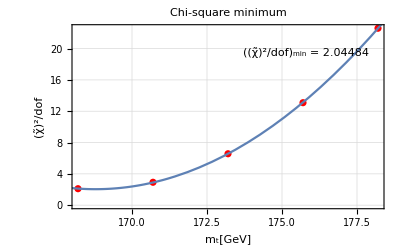

168.715±2.08124

0.276181

0.276137

0.284916

0.541242

6.45324×10^-6

83871.4

33543.2

```mathematica
CHI SQUARE STUFF;

chisquarebin[pvalue_,perror_,int_,mass_]:=(pvalue[[int]]-fitting[[int]][mass])^2/(perror[[int]]^2);
sumchisquare[pvalue_,perror_,mass_]:=Sum[chisquarebin[pvalue,perror,i,mass],{i,1,Length[pvalue]-1}];
chitilde[pvalue_,perror_,mass_]:=sumchisquare[pvalue,perror,mass]/(Length[pvalue]-1)
minchitilde[pvalue_,perror_]:=x/.Last[FindMinimum[chitilde[pvalue,perror,x],{x,168.2,178.2}]]
chidata=ParallelTable[{mass[[j]],Table[chitilde[valuep,errorp,mass[[i]]],{i,1,nmass}][[j]]},{j,1,nmass}];
chifunc=LinearModelFit[chidata,{1,x,x^2},x];
minimumx=minchitilde[valuep,errorp]
x/.Last[FindMinimum[{Normal[chifunc],162.8≤ x≤ 178.2},{x,168.2}]]
chivaluebnd=chitilde[valuep,errorp,minimumx]+1
(*deltamassbound=x/.Solve[chitilde[valuep,errorp,x]==chivaluebound,x]*) (*finding the corresponding m value for given chi square value without divide by dof*)
deltamassbnd=x/.Solve[Normal[chifunc]==chivaluebnd,x]
deltam1=Mean[Abs[minimumx-deltamassbnd]]
chiparabola=Show[ListPlot[chidata,FrameLabel-> {"m_t[GeV]","(χ̃)^2/dof"},PlotTheme->"Detailed",PlotStyle->Red],Plot[Normal[chifunc],{x,160,180}],PlotLabel->"Chi-square minimum",Epilog-> Inset[Framed[Style["((χ̃)^2/dof)_min = " <> ToString[chitilde[valuep,errorp,minimumx]]],Background->White],Scaled[{.75,.85}]]]
PlusMinus[minimumx,deltam1]

fitting[[1]][173.2]
value[[1,3,2]]
valuep[[1]]

(fitting[[1]][3]-valuep[[1]])^2
errorp[[1]]^2

(fitting[[1]][3]-valuep[[1]])^2/(errorp[[1]]^2)
sumchisquare[valuep,errorp,3]/18
```

```mathematica
BEFORE DIVIDED BY DEGREE OF FREEDOMS (EXTRACTING ONE DELTA MASS);
```

168.715

35.7623

{168.265,169.295}

{0.450046,-0.580462}

0.515254

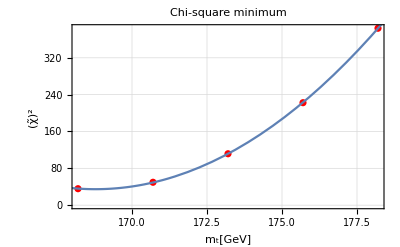

168.715±0.515254

```mathematica
minchitilderaw[pvalue_,perror_]:=x/.Last[FindMinimum[sumchisquare[pvalue,perror,x],{x,168.2,178.2}]]
mmiddle=minchitilderaw[valuep,errorp]
chidataraw=ParallelTable[{mass[[j]],Table[sumchisquare[valuep,errorp,mass[[i]]],{i,1,nmass}][[j]]},{j,1,nmass}];
chifuncraw=LinearModelFit[chidataraw,{1,x,x^2},x];
chivaluebound=sumchisquare[valuep,errorp,mmiddle]+1
(*deltamassbound=x/.Solve[chitilde[valuep,errorp,x]==chivaluebound,x]*) (*finding the corresponding m value for given chi square value without divide by dof*)
deltamassbound=x/.Solve[Normal[chifuncraw]==chivaluebound,x]
mmiddle-deltamassbound
deltamone=Mean[Abs[mmiddle-deltamassbound]]
chiparabolaraw=Show[ListPlot[chidataraw,FrameLabel-> {"m_t[GeV]","(χ̃)^2"},PlotTheme->"Detailed",PlotStyle->Red],Plot[Normal[chifuncraw],{x,160,180}],PlotLabel->"Chi-square minimum"]
PlusMinus[mmiddle,deltamone]
```

{163.46,165.049,167.326,170.045,172.095}

{1.24556,0.8117,0.192399,0.589576,0.571207}

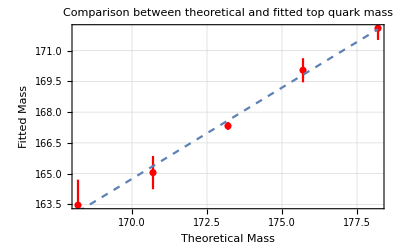

```mathematica
FITTED MASS ;
EXTRACTION OF MASS AND DELTA MASS OF TOP QUARK FOR ONE PSEUDO EXPERIMENTS;
fittingmass[nevents_,m_]:=Reap[
Block[{pvaluelist,perrorlist,zeropos,datachi,chisq,mout,result,chisqraw,datachiraw,fchiraw,chibound,deltambound,deltameins,fchi},
pvaluelist=valsnormpseudo[nevents][[m]];
perrorlist=errnormpseudo[nevents][[m]] ;
zeropos=Position[perrorlist,0.]; 
perrorlist=Delete[perrorlist,zeropos]; (*delete zero error values*)
pvaluelist=Delete[pvaluelist,zeropos];
chisq=ParallelTable[chitilde[pvaluelist,perrorlist,mass[[i]]],{i,1,nmass}];
chisqraw=ParallelTable[sumchisquare[pvaluelist,perrorlist,mass[[i]]],{i,1,nmass}];
datachi=ParallelTable[{mass[[j]],chisq[[j]]},{j,1,nmass}];
datachiraw=ParallelTable[{mass[[j]],chisqraw[[j]]},{j,1,nmass}];
fchiraw=LinearModelFit[datachiraw,{1,x,x^2},x];
(*fchi=Fit[datachi,{1,x,x^2},x];
mout=x/.Last[FindMinimum[{Normal[fchiraw],162.8≤ x≤ 178.2},{x,168.2}]];*)
mout=minchitilderaw[pvaluelist,perrorlist];
chibound=sumchisquare[pvaluelist,perrorlist,minchitilderaw[pvaluelist,perrorlist]]+1;
deltambound=x/.Solve[Normal[fchiraw]==chibound,x];
deltameins=Mean[Abs[mout-deltambound]];
result=Sow[{mout,deltameins}]
]
][[2,1]];

massfit=Reap[Do[Sow[fittingmass[stdnevents,i]],{i,1,nmass,1}]][[2,1]];
masschi=Reap[Do[Sow[Flatten[massfit[[i]],1]],{i,1,nmass,1}]][[2,1]];
fitmass=masschi[[All,1]]
fitmasserr=masschi[[All,2]]

PLOTTING THE THEORETICAL MASS AND THE MASS FROM CHI SQUARE + 1 ANALYSIS  FROM ONE PSEUDO EXPERIMENTS(NO BIASED);
fitmassplot=ErrorListPlot[Table[{{mass[[i]],fitmass[[i]]},ErrorBar[fitmasserr[[i]]]},{i,1,nmass}],PlotTheme->"Detailed",PlotStyle->Red];
fitmassfunc=Fit[Table[{mass[[i]],fitmass[[i]]},{i,1,nmass}],{1,x},x];
fittmass=Show[fitmassplot,Plot[fitmassfunc,{x,168.2,178.2},PlotStyle->Dashed],PlotTheme->"Detailed",FrameLabel-> { "Theoretical Mass","Fitted Mass"},PlotLabel-> "Comparison between theoretical and fitted top quark mass"]
```

```mathematica
N -PSEUDO EXPERIMENTS;
```

```mathematica
npseudoexp[nevents_,n_]:=Partition[Reap[
For[k=1,k<n+1,k++,
Block[{pvaluelist,perrorlist,zeropos,chisq,datachi,fchi,mout,chisqmin,result},
pvaluelist=valsnormpseudo[nevents][[number]];
perrorlist=errnormpseudo[nevents][[number]] ;
zeropos=Position[perrorlist,0.]; 
perrorlist=Delete[perrorlist,zeropos]; (*delete zero error values*)
pvaluelist=Delete[pvaluelist,zeropos];
chisq=ParallelTable[chitilde[pvaluelist,perrorlist,mass[[i]]],{i,1,nmass}];
datachi=ParallelTable[{mass[[j]],chisq[[j]]},{j,1,nmass}];
(*fchi=Fit[datachi,{1,x,x^2},x];
mout=x/.Last[FindMinimum[{fchi,162.8≤ x≤ 178.2},{x,168.2}]];*)
mout=minchitilderaw[pvaluelist,perrorlist];
chisqmin=chitilde[pvaluelist,perrorlist,mout];
result=Sow[{mout,chisqmin}]
]
];
][[2,1]],n];
exp=Reap[Sow[npseudoexp[stdnevents,npseudo]]][[2,1,1,1]];
```

```mathematica
SOME STATISTICS AND  HISTOGRAMS ABOUT PSEUDO EXPERIMENT;
```

{1.13889,1.17511,1.21671,1.35374,1.4127,1.44101,1.55629,1.66661,1.69793,1.72435,1.74061,1.79292,1.79527,1.87522,1.91737,1.91986,1.99352,1.99662,2.05928,2.08822,2.08979,2.09491,2.09558,2.10327,2.10927,2.14296,2.15642,2.24832,2.28031,2.31761,2.33681,2.34461,2.42159,2.43249,2.46551,2.47501,2.47939,2.48979,2.52311,2.53329,2.53456,2.5423,2.54567,2.54982,2.56143,2.56648,2.59307,2.59648,2.60366,2.61794,2.67243,2.68664,2.73827,2.76868,2.83429,2.84885,2.86779,2.88683,2.90166,2.91887,2.936,2.94511,2.97723,3.00339,3.03864,3.04841,3.14132,3.1794,3.18574,3.19256,3.23671,3.28493,3.3065,3.32209,3.3698,3.37149,3.37409,3.38645,3.42097,3.42257,3.42416,3.45133,3.51335,3.51572,3.62856,3.63999,3.7109,3.72996,3.75391,3.8529,3.86707,3.91358,3.93324,3.96544,4.00435,4.11244,4.45131,4.73371,4.79507,5.99515}

20

{{167.413,1.13889},{167.178,1.17511},{167.536,1.21671},{167.773,1.35374},{167.719,1.4127},{168.508,1.44101},{167.211,1.55629},{168.303,1.66661},{166.58,1.69793},{167.987,1.72435},{167.913,1.74061},{167.731,1.79292},{168.105,1.79527},{167.153,1.87522},{168.284,1.91737},{166.997,1.91986},{167.835,1.99352},{168.198,1.99662},{167.513,2.05928},{167.486,2.08822},{166.465,2.08979},{167.937,2.09491},{168.253,2.09558},{167.615,2.10327},{166.665,2.10927},{168.231,2.14296},{166.712,2.15642},{166.874,2.24832},{166.64,2.28031},{166.712,2.31761},{168.373,2.33681},{167.992,2.34461},{167.458,2.42159},{167.464,2.43249},{168.444,2.46551},{167.539,2.47501},{168.364,2.47939},{168.046,2.48979},{167.41,2.52311},{168.01,2.53329},{167.255,2.53456},{168.186,2.5423},{167.743,2.54567},{168.8,2.54982},{167.09,2.56143},{168.069,2.56648},{168.348,2.59307},{168.883,2.59648},{167.84,2.60366},{167.339,2.61794},{168.018,2.67243},{167.865,2.68664},{167.639,2.73827},{168.712,2.76868},{168.285,2.83429},{167.776,2.84885},{169.051,2.86779},{168.122,2.88683},{168.665,2.90166},{168.2,2.91887},{167.375,2.936},{167.891,2.94511},{167.466,2.97723},{167.621,3.00339},{166.789,3.03864},{167.782,3.04841},{168.788,3.14132},{167.569,3.1794},{168.465,3.18574},{167.953,3.19256},{167.869,3.23671},{168.019,3.28493},{167.333,3.3065},{167.103,3.32209},{167.848,3.3698},{168.155,3.37149},{167.958,3.37409},{168.041,3.38645},{167.881,3.42097},{167.775,3.42257},{167.465,3.42416},{167.354,3.45133},{168.657,3.51335},{167.911,3.51572},{167.581,3.62856},{167.124,3.63999},{167.451,3.7109},{167.282,3.72996},{168.313,3.75391},{167.647,3.8529},{167.373,3.86707},{167.904,3.91358},{167.84,3.93324},{169.397,3.96544},{169.038,4.00435},{167.534,4.11244},{166.931,4.45131},{167.952,4.73371},{169.187,4.79507},{168.034,5.99515}}

100

167.802

{0.019958,0.0253579,0.0270589,0.0283879,0.0335088,0.0378018,0.0385289,0.0459508,0.0588517,0.0634024,0.0673485,0.0708147,0.0793895,0.0825495,0.0894236,0.102681,0.109195,0.111465,0.135359,0.150664,0.151563,0.154414,0.155832,0.162621,0.181036,0.184982,0.186828,0.18987,0.20831,0.216267,0.217313,0.220637,0.232323,0.232384,0.239397,0.244004,0.262634,0.265621,0.267334,0.267651,0.288686,0.302808,0.315662,0.320724,0.336162,0.336629,0.337416,0.343763,0.350684,0.3537,0.383819,0.388568,0.39125,0.39592,0.398088,0.426388,0.428554,0.429238,0.447387,0.451737,0.462633,0.468625,0.482747,0.483432,0.501686,0.510969,0.52014,0.546351,0.546705,0.562471,0.571051,0.590883,0.623676,0.642127,0.648466,0.663087,0.677715,0.698253,0.706312,0.712046,0.804665,0.855429,0.863354,0.870639,0.910355,0.92801,0.986635,0.998122,1.01323,1.08139,1.0897,1.08989,1.13717,1.16146,1.22217,1.23614,1.24901,1.33625,1.38534,1.59562}

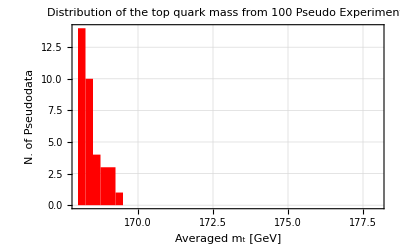

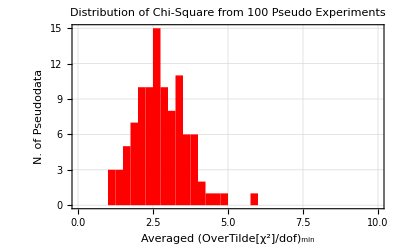

False

Theory, LO QCD | Variable | Luminosity [fb^-1] | m_t±δm_t[GeV] | Averaged ((χ̃)^2/dof)_min | Probability p-value | m_t^in-m_t^out [GeV]
Full, μ_0=mt | p_(T, b) average | 35 | 167.802±0.546351 | 2.77674 | 0.000113508 | 5.39826

```mathematica
(*pexpmass=Delete[Sort[exp[[All,1]]],Partition[(-1)*Range[11],1]]; (*96 percent of the mass data *)
pexpchisq=Delete[Sort[exp[[All,2]]],Partition[(-1)*Range[11],1]] (*96 percent of the chi square min data due to isolated big value of chi*)*)

pexpchisq=Sort[exp[[All,2]]]

ELIMINATE THI  CHI-SQUARE THAT IS MORE THAN CHI SQUARE STANDARD FOR ET2;
chistandard=20
newexp=Reap[Do[
Which[scalename[[k]]=="et2",
If[(pexpchisq[[i]]<chistandard)&&(pexpchisq[[i]]==exp[[j,2]]),Sow[{exp[[j,1]],exp[[j,2]]}],Nothing],
scalename[[k]]=="mt",
Nothing],
{k,1,Length[scalename],1},{i,1,Length[pexpchisq],1},{j,1,Length[exp],1}]][[2,1]]
Length[newexp]
pexpmass=newexp[[All,1]];
pexpchis=newexp[[All,2]];


massout=Mean[pexpmass]

stddeviations=Reap[Do[
Sow[StandardDeviation[exp[[All,1]]]],
{i,1,Length[exp],1}]][[2,1]];

deltamassout=Reap[Block[{sortedmass,variance},
sortedmass=pexpmass;
variance=Sort[Reap[Do[Sow[Abs[sortedmass[[i]]-Mean[sortedmass]]],{i,1,Length[sortedmass],1}]][[2,1]]]; (*sorted the spread of the data from the mean*)
Print[variance];
Sow[variance[[Round[68*Length[sortedmass]/100]]]] (*take the 68% CL i.e take the 68%*Number-th of the data as the error*)
]][[2,1,1]];

chiout=Mean[pexpchis];


pexpmasshist=Histogram[pexpmass,{168,178,0.25},PlotTheme->"Detailed",FrameLabel->{"Averaged m_t [GeV]","N. of Pseudodata"},ChartBaseStyle->EdgeForm[None], ChartStyle->Red, PlotLabel-> "Distribution of the top quark mass from " <>ToString[Length[pexpchis]]<>" Pseudo Experiments"]
pexpchisqhist=Histogram[pexpchis,{0,10,0.25},PlotTheme->"Detailed",FrameLabel-> {"Averaged (OverTilde[χ^2]/dof)_min", "N. of Pseudodata"},ChartBaseStyle->EdgeForm[None], ChartStyle->Red,PlotLabel-> "Distribution of Chi-Square from "<>ToString[Length[pexpchis]]<>" Pseudo Experiments"]

SOME RESULTS;

pvalue[pvalue_]:= ChiSquarePValue[chiout*(Length[pvalue]-1),Length[pvalue]-1][[2]];
pvout=pvalue[valuep];
pvout>pvaluestandard
(*stddeviations=(Abs[massout[[number]]]*Sqrt[Length[pexpmass]/2])/InverseErfc[pvout]*10^-3*)
deltam=mass[[number]]-massout;
result=Grid[{{"Theory, LO QCD", "Variable","Luminosity [fb^-1]",ToString[PlusMinus[Subscript[m, t],Subscript[δm, t]],StandardForm]<>"[GeV]", "Averaged ((χ̃)^2/dof)_min","Probability p-value","m_t^in-m_t^out [GeV]"},
{StringForm["Full, μ_0=``",scale[[int]]],variable[[numbofdiffdist]],luminosity,PlusMinus[N[massout,2],N[deltamassout,2]],chiout,pvout ,deltam}},Frame->All]
```

```mathematica
EXPORTING FIGURES;
```

```mathematica
Export[varname[[numbofdiffdist]]<>"_"<>scalename[[int]]<>"_"<>ToString[luminosity]<>"_pseudodata.pdf",pt1];
Export[varname[[numbofdiffdist]]<>"_"<>scalename[[int]]<>"_"<>ToString[luminosity]<>"_parabola_chi_square.pdf",chiparabola];
Export[varname[[numbofdiffdist]]<>"_"<>scalename[[int]]<>"_"<>ToString[luminosity]<>"_pseudo_exp_mass_averaged.pdf", pexpmasshist];
Export[varname[[numbofdiffdist]]<>"_"<>scalename[[int]]<>"_"<>ToString[luminosity]<>"_pseudo_exp_chi_square_averaged.pdf",pexpchisqhist];
Export[varname[[numbofdiffdist]]<>"_"<>scalename[[int]]<>"_"<>ToString[luminosity]<>"_mass_fitting.pdf", fittmass];
Export[varname[[numbofdiffdist]]<>"_"<>scalename[[int]]<>"_"<>ToString[luminosity]<>"_result_table.pdf", result];
```

```mathematica
GATHERING DATA;
If[luminosity==5,
Do[
Export["kdata_"<>ToString[varname[[numbofdiffdist]]]<>"_"<>ToString[nbins]<>"_"<>massname[[i]]<>"_"<>scalename[[int]]<>".txt",Transpose[{bins[[i]],valhelac[[i]]}],"Table"],
{i,1,nmass,1}
],
Nothing
]
```

Nothing